```mathematica
TransMatrixFlint[β_,ϵ_,f_,p_]:=Module[{points,g,mtx},points=Range[0,6/ϵ ,ϵ];
(*connect points up into a linear graph*)g=RelationGraph[Abs[#1-#2]==ϵ&,points,DirectedEdges->True];
(*set edge weights*)g=With[{el=EdgeList[g]},Graph[el,EdgeWeight->(#->p[#[[1]],#[[2]],β,ϵ,f]&/@el)]];
(*get the weight matrix*)mtx=WeightedAdjacencyMatrix[g];
(*need to make up the difference for cases when x==y if row is not normalized*)mtx+DiagonalMatrix[1-Total/@mtx]]


TransMatrixFlintNN[β_,ϵ_,f_,p_]:=Module[{points,g,mtx},points=Range[0,6/ϵ ,ϵ];
(*connect points up into a linear graph*)g=RelationGraph[Abs[#1-#2]==ϵ&,points,DirectedEdges->True];
(*set edge weights*)g=With[{el=EdgeList[g]},Graph[el,EdgeWeight->(#->p[#[[1]],#[[2]],β,ϵ,f]&/@el)]];
(*get the weight matrix*)mtx=WeightedAdjacencyMatrix[g];
(*need to make up the difference for cases when x==y if row is not normalized mtx+DiagonalMatrix[1.-Total/@mtx]*) mtx]
```

```mathematica
zeta = 1
points=Range[0,6,zeta];
```

1

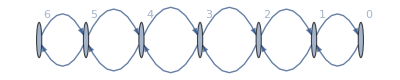

```mathematica
g=RelationGraph[Abs[#1-#2]==zeta&,points,DirectedEdges->True]
```

```mathematica
edgelis=EdgeList[g]
```

{0->1,1->0,1->2,2->1,2->3,3->2,3->4,4->3,4->5,5->4,5->6,6->5}

(8 √2)/3

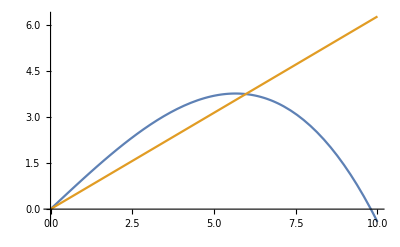

{{0.999994,6.36497×10^-6,0.,0.,0.,0.,0.},{0.000333333,0.999658,8.17278×10^-6,0.,0.,0.,0.},{0.,0.000333333,0.999653,0.0000134746,0.,0.,0.},{0.,0.,0.000333333,0.999638,0.0000285258,0.,0.},{0.,0.,0.,0.000333333,0.999589,0.0000775412,0.},{0.,0.,0.,0.,0.000333333,0.999396,0.000270645},{0.,0.,0.,0.,0.,0.000333333,0.999667}}

```mathematica
f[x_]:=-x^3*(1/2)^2/24+x
ccrit =2* Sqrt[8];
Ecrit = f[ccrit]

f1[x_]:=(Ecrit/6)*x;
f3[x_]:=((1/2)*x^2-1)*(1/2)*x^2;
Plot[{f[x],f1[x]},{x,0,10}]



p[x_,y_,β_,ϵ_,f_]:=If[Abs[y-x]≠ϵ,0,Piecewise[{{1/3000,f[y]<f[x]},{1/3000 Exp[(f[x]-f[y])/β],f[y]>f[x]}},0]]

temperatures={25/100,30/100,35/100,40/100, 50/100,60/100};

(*use rationals here for best precision*)
trmtx=TransMatrixFlint[0.25,1,f,p]
```

```mathematica
test[β_,ϵ_,f_,p_]:=Table[p[i,j,β,ϵ,f],{i,Range[0,6 ,ϵ]}, {j,Range[0,6 ,ϵ]}];
```

```mathematica
test[0.25,0.1,f,p];
```

```mathematica
TransMatrixMM[β_,ϵ_,f_,p_]:= test[β,ϵ,f,p] + DiagonalMatrix[1 - Total[test[0.25,ϵ,f,p],{2}]];
TransMatrixMM[0.25,1,f,p]//MatrixForm
TransMatrixFlint[0.25,1,f,p]//MatrixForm
Total[TransMatrixMM[0.25,1.,f,p],{2}]
Total[TransMatrixFlint[0.25,1.,f,p],{2}]
Total[trmtx,{2}]

p[0,1,0.25,1,f];
test[0.25,1,f,p]//MatrixForm;
```

(0.999994 | 6.36497×10^-6 | 0. | 0. | 0. | 0. | 0.
0.000333333 | 0.999658 | 8.17278×10^-6 | 0. | 0. | 0. | 0.
0. | 0.000333333 | 0.999653 | 0.0000134746 | 0. | 0. | 0.
0. | 0. | 0.000333333 | 0.999638 | 0.0000285258 | 0. | 0.
0. | 0. | 0. | 0.000333333 | 0.999589 | 0.0000775412 | 0.
0. | 0. | 0. | 0. | 0.000333333 | 0.999396 | 0.000270645
0. | 0. | 0. | 0. | 0. | 0.000333333 | 0.999667)

(0.999994 | 6.36497×10^-6 | 0. | 0. | 0. | 0. | 0.
0.000333333 | 0.999658 | 8.17278×10^-6 | 0. | 0. | 0. | 0.
0. | 0.000333333 | 0.999653 | 0.0000134746 | 0. | 0. | 0.
0. | 0. | 0.000333333 | 0.999638 | 0.0000285258 | 0. | 0.
0. | 0. | 0. | 0.000333333 | 0.999589 | 0.0000775412 | 0.
0. | 0. | 0. | 0. | 0.000333333 | 0.999396 | 0.000270645
0. | 0. | 0. | 0. | 0. | 0.000333333 | 0.999667)

{1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.}

{1.,1.,1.,1.,1.,1.,1.}

```mathematica
(*MatrixPlot[trmtx]*)
(*use a high precision on trmtx*)
A=DiscreteMarkovProcess[1,SetPrecision[trmtx,80]];
A1=DiscreteMarkovProcess[1,SetPrecision[trmtx1,80]];

EscTime=FirstPassageTimeDistribution[A,7];
EscTime1=FirstPassageTimeDistribution[A1,7];

Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,SetPrecision[TransMatrixFlint[0.25,1,f,p],120]],7]]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

2.01746437440162288164662730999222846026256551591749879378423593459757735369242924382720696×10^10

```mathematica
(Log[Mean[EscTime1]]-Log[Mean[EscTime]])/(1/temperatures[[2]]-1/temperatures[[1]])
```

DiscreteMarkovProcess::bprm: The parameters of distribution DiscreteMarkovProcess[1,trmtx1] are not valid. Use DistributionParameterAssumptions to obtain the parameter assumptions.

-3/2 (-23.7276923926573558045494431792764232854983160123608+Log[Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,trmtx1],7]]])

```mathematica
arrhenius[func_, temp_, eps_]:=Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,SetPrecision[TransMatrixFlint[temp,eps,func,p],120]], 6]]
arrheniusMM[func_, temp_, eps_]:=Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,SetPrecision[TransMatrixMM[temp,eps,func,p],120]], 6]]
```

```mathematica
{arrheniusMM[f, 0.25, 1],arrhenius[f, 0.25, 1]}
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

{1.01755302168078116723707453516896775585448148737498584024185304017285759435182934099838127775×10^10,1.01755302168078116723707453516896775585448148737498584024185304017285759435182934099838127775×10^10}

```mathematica
Total[TransMatrixMM[0.25,1,f,p]]
arrheniusMM[f, 0.25, 1]
```

{1.00033,0.999998,0.999995,0.999985,0.999951,0.999807,0.999937}

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

1.01755302168078116723707453516896775585448148737498584024185304017285759435182934099838127775×10^10

```mathematica
Table[arrhenius[f, i,1],{i,temperatures}]
```

{1.017553021680780845652133246134133029577986256147515308258432385187481940106466361128946709265×10^10,9.40246550440559050406809832417195883293501161963352200418372585272255762988212068894914123118×10^8,1.75757345855100060609585452519190461858295681395990884545033432543773562941835822945388381383094×10^8,5.09785398948774496281340307969351347065559065275779130394453686646252372594117069635258900542887×10^7,9.419817753144918347926568097069577697069243325058028688060064081576389878531369314002768269994163×10^6,3.1896782612788756131377754407534972865070322706234433536946967173077588069097002761382235750491723×10^6}

```mathematica
arrhenius[f,#,1]&/@temperatures
```

{1.017553021680780845652133246134133029577986256147515308258432385187481940106466361128946709265×10^10,9.40246550440559050406809832417195883293501161963352200418372585272255762988212068894914123118×10^8,1.75757345855100060609585452519190461858295681395990884545033432543773562941835822945388381383094×10^8,5.09785398948774496281340307969351347065559065275779130394453686646252372594117069635258900542887×10^7,9.419817753144918347926568097069577697069243325058028688060064081576389878531369314002768269994163×10^6,3.1896782612788756131377754407534972865070322706234433536946967173077588069097002761382235750491723×10^6}

```mathematica
Table[arrhenius[f,x,1],{x,temperatures}]
```

{1.017553021680780845652133246134133029577986256147515308258432385187481940106466361128946709265×10^10,9.40246550440559050406809832417195883293501161963352200418372585272255762988212068894914123118×10^8,1.75757345855100060609585452519190461858295681395990884545033432543773562941835822945388381383094×10^8,5.09785398948774496281340307969351347065559065275779130394453686646252372594117069635258900542887×10^7,9.419817753144918347926568097069577697069243325058028688060064081576389878531369314002768269994163×10^6,3.1896782612788756131377754407534972865070322706234433536946967173077588069097002761382235750491723×10^6}

```mathematica
functions={f,f1}
```

{f,f1}

```mathematica
res = Table[arrhenius[f,x,1],{f,functions},{x,temperatures}];
```

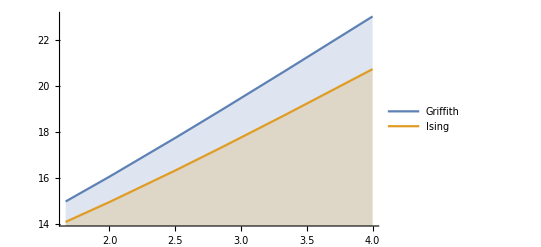

```mathematica
ListLinePlot[{Transpose[{1/temperatures,Log[res[[1]]]}], Transpose[{1/temperatures,Log[res[[2]]]}]},PlotLegends->{"Griffith","Ising"}, Filling->Axis]
```

```mathematica
functest[x_]:=x^2
```

```mathematica
func [fava,2]
```

func[fava,2]

```mathematica
listval = {1,2,3}
```

{1,2,3}

```mathematica
ClearAll
```

ClearAll

```mathematica
listfuncobs={ #&, #^2&}
```

{#1&,#1^2&}

```mathematica
listfunc={SetDelayed[x[x],x^2[x]]}
```

{Null}

```mathematica
listfunc="g"<>ToString[#]&/@{1,2,3}//ToExpression;
```

```mathematica
tem=Developer`ToPackedArray[{0.05,0.06,0.2,0.35,0.5}];
```

```mathematica
tempes = {1,0.95, 0.9,0.85,0.8,0.75,0.7,0.6}
tempes1 = {1,0.95, 0.9,0.85,0.8,0.75,0.7,0.6,0.5,0.4,0.3}
```

{1,0.95,0.9,0.85,0.8,0.75,0.7,0.6}

{1,0.95,0.9,0.85,0.8,0.75,0.7,0.6,0.5,0.4,0.3}

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

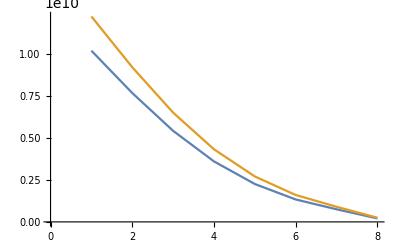

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

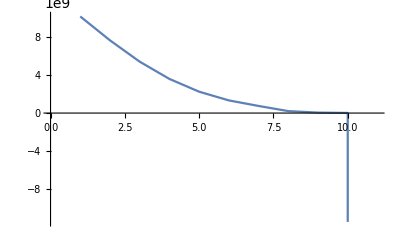

```mathematica
ListLinePlot[{arrhenius[f,0.25,#]&/@tempes, 1.2*arrheniusMM[f,0.25,#]&/@tempes}]
ListLinePlot[arrheniusMM[f,0.25,#]&/@tempes1]
```

```mathematica
m = TransMatrixFlint[0.25,1,f,p]
```

{{0.999994,6.36497×10^-6,0.,0.,0.,0.,0.},{0.000333333,0.999658,8.17278×10^-6,0.,0.,0.,0.},{0.,0.000333333,0.999653,0.0000134746,0.,0.,0.},{0.,0.,0.000333333,0.999638,0.0000285258,0.,0.},{0.,0.,0.,0.000333333,0.999589,0.0000775412,0.},{0.,0.,0.,0.,0.000333333,0.999396,0.000270645},{0.,0.,0.,0.,0.,0.000333333,0.999667}}

```mathematica
Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,SetPrecision[TransMatrixFlint[0.25,1,f,p],120]],7]]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

2.01746437440162288164662730999222846026256551591749879378423593459757735369242924382720696×10^10

```mathematica
m//MatrixForm
```

(0.999994 | 6.36497×10^-6 | 0. | 0. | 0. | 0. | 0.
0.000333333 | 0.999658 | 8.17278×10^-6 | 0. | 0. | 0. | 0.
0. | 0.000333333 | 0.999653 | 0.0000134746 | 0. | 0. | 0.
0. | 0. | 0.000333333 | 0.999638 | 0.0000285258 | 0. | 0.
0. | 0. | 0. | 0.000333333 | 0.999589 | 0.0000775412 | 0.
0. | 0. | 0. | 0. | 0.000333333 | 0.999396 | 0.000270645
0. | 0. | 0. | 0. | 0. | 0.000333333 | 0.999667)

```mathematica
mdrop = Delete[m,-1]
```

{{0.999994,6.36497×10^-6,0.,0.,0.,0.,0.},{0.000333333,0.999658,8.17278×10^-6,0.,0.,0.,0.},{0.,0.000333333,0.999653,0.0000134746,0.,0.,0.},{0.,0.,0.000333333,0.999638,0.0000285258,0.,0.},{0.,0.,0.,0.000333333,0.999589,0.0000775412,0.},{0.,0.,0.,0.,0.000333333,0.999396,0.000270645}}

```mathematica
mdrop//MatrixForm
```

(0.999994 | 6.36497×10^-6 | 0. | 0. | 0. | 0. | 0.
0.000333333 | 0.999658 | 8.17278×10^-6 | 0. | 0. | 0. | 0.
0. | 0.000333333 | 0.999653 | 0.0000134746 | 0. | 0. | 0.
0. | 0. | 0.000333333 | 0.999638 | 0.0000285258 | 0. | 0.
0. | 0. | 0. | 0.000333333 | 0.999589 | 0.0000775412 | 0.
0. | 0. | 0. | 0. | 0.000333333 | 0.999396 | 0.000270645)

```mathematica
diag = Delete[DiagonalMatrix[Table[1,{i,1,7}]],-1]
```

{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0}}

```mathematica
diag//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
LinearSolve[-mdrop + diag,Table[-1,{i,1,6}]]
```

{-4.6546×10^9,-4.65445×10^9,-4.64791×10^9,-4.4863×10^9,-2.59771×10^9,5.52093×10^9,1.552×10^10}

```mathematica
Mean[FirstPassageTimeDistribution[DiscreteMarkovProcess[1,SetPrecision[TransMatrixFlint[0.25,1,f,p],120]],7]]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

2.01746437440162288164662730999222846026256551591749879378423593459757735369242924382720696×10^10

```mathematica
LinearSolve[- TransMatrixFlint[0.25,1,f,p][[;;-2,;;-2]]+ DiagonalMatrix[Table[1,{i,1,6}]],Table[1,{i,1,6}]]
```

{2.01746×10^10,2.01745×10^10,2.0168×10^10,2.00063×10^10,1.81177×10^10,9.99911×10^9}

```mathematica
escapeTimes[beta_,eps_,f_]:=LinearSolve[- TransMatrixFlint[beta,eps,f,p][[;;-2,;;-2]]+ DiagonalMatrix[Table[1,{i,1,6}]],Table[1,{i,1,6}]][[1]]
```

```mathematica
escapeTimes[0.35,1,f]
```

3.19361×10^8

```mathematica
LinearSolve[- TransMatrixFlint[0.25,1,f,p][[;;-2,;;-2]]+ DiagonalMatrix[Table[1,{i,1,6}]],Table[1,{i,1,6}]]
```

{2.01746×10^10,2.01745×10^10,2.0168×10^10,2.00063×10^10,1.81177×10^10,9.99911×10^9}

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

General::stop: Further output of DiscreteMarkovProcess::dmnorm will be suppressed during this calculation.

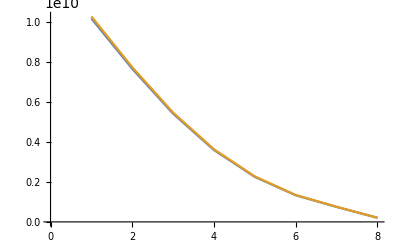

```mathematica
ListLinePlot[{arrhenius[f,0.25,#]&/@tempes, 1.01*arrheniusMM[f,0.25,#]&/@tempes}]
```

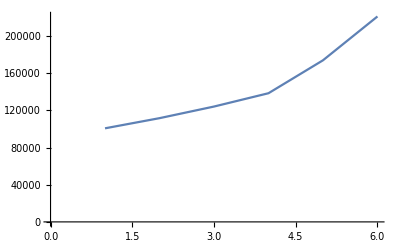

```mathematica
ListLinePlot[escapeTimes[#,1,f]&/@(1/temperatures)]
```

```mathematica
escapeTimes[#,1,f]&/@temperatures//N
```

{2.01746×10^10,1.77645×10^9,3.19361×10^8,8.96732×10^7,1.57447×10^7,5.13209×10^6}

```mathematica
Log[res[[1]]]
```

{23.043251676677384639087671086689598232470104575747168751784356423995280084405160395450550301047,20.6616526865396400758776237644912543883024256427557599711044222245956908881891038773501246491516,18.98461488496563905447960665193912107324574614199136479575489959987747256526332599788076056421446,17.74691531575821841833814508755561413642807160537722321332276737355026966504516129790757193195056,16.058326299565491536377010915775350395665677357531669796745875777408118497308250041125752824570096,14.9754306111411955895191106377966023253051842069541001536821290439646347491653511491806190175122048}

```mathematica
escapeTimes[#,1,f]&/@temperatures//N
```

{2.01746×10^10,1.77645×10^9,3.19361×10^8,8.96732×10^7,1.57447×10^7,5.13209×10^6}

```mathematica
Transpose[{1/temperatures,escapeTimes[#,1,f]&/@temperatures//N}]
```

{{4,2.01746×10^10},{10/3,1.77645×10^9},{20/7,3.19361×10^8},{5/2,8.96732×10^7},{2,1.57447×10^7},{5/3,5.13209×10^6}}

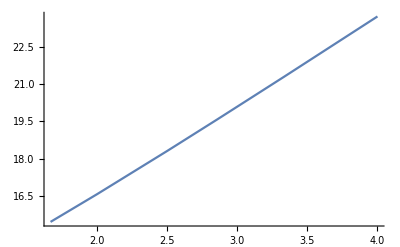

```mathematica
ListLinePlot[Transpose[{1/temperatures,Log[escapeTimes[#,1,f]&/@temperatures]}]]
```